## Pre

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation

```mathematica
Get["../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
?dispersion`*
```

```mathematica
pltcolors=ColorData[97,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Needs["PolygonPlotMarkers`"]
```

```mathematica
(1+g[#])&/@{a,b,c}
```

{1+g[a],1+g[b],1+g[c]}

```mathematica
shapes=PolygonMarker[All];
shapesTip=Table[
Tooltip[Graphics[{FaceForm[pltcolors[[i]]],EdgeForm[{Black,Thickness[0.003],JoinForm["Miter"]}],PolygonMarker[shapes[[i]],Scaled[.3]]},ImageSize->15],shapes[[i]]],
{i,1,Length@pltcolors}]
shapesTipTable={shapesTip,
Table[i,{i,1,Length@pltcolors}]}//Transpose
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,7},{-Graphics-,8},{-Graphics-,9},{-Graphics-,10},{-Graphics-,11},{-Graphics-,12},{-Graphics-,13},{-Graphics-,14},{-Graphics-,15}}

```mathematica
pltmarkers={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Polarization Tensor

```mathematica
?v
```

dispersion`v

v[theta_,phi_]:={1,Cos[phi] Sin[theta],Sin[phi] Sin[theta],Cos[theta]}

```mathematica
v[theta,phi]
```

{1,Cos[phi] Sin[theta],Sin[phi] Sin[theta],Cos[theta]}

```mathematica
vvMatrix[theta,phi];
%//MatrixForm
```

(1 | Cos[phi] Sin[theta] | Sin[phi] Sin[theta] | Cos[theta]
Cos[phi] Sin[theta] | Cos[phi]^2 Sin[theta]^2 | Cos[phi] Sin[phi] Sin[theta]^2 | Cos[phi] Cos[theta] Sin[theta]
Sin[phi] Sin[theta] | Cos[phi] Sin[phi] Sin[theta]^2 | Sin[phi]^2 Sin[theta]^2 | Cos[theta] Sin[phi] Sin[theta]
Cos[theta] | Cos[phi] Cos[theta] Sin[theta] | Cos[theta] Sin[phi] Sin[theta] | Cos[theta]^2)

```mathematica
intFun[n_]:=Integrate[,{x}]
```

```mathematica
nMatrixAxial[integrals_:{I0,I1,I2}]:=Module[{thetaM,phiM},
thetaM=theta;
phiM=phi;


{
{2I0,0,0,-2I1},
{0,-(I0-I2),0,0},
{0,0,-(I0-I2),0},
{2I1,0,0,-2I2}
}/4

]
```

```mathematica
nMatrixAxial[];
%//MatrixForm
```

(I0/2 | 0 | 0 | -I1/2
0 | 1/4 (-I0+I2) | 0 | 0
0 | 0 | 1/4 (-I0+I2) | 0
I1/2 | 0 | 0 | -I2/2)

```mathematica
Eigensystem@nMatrixAxial[]//MatrixForm//FullSimplify
```

(1/4 (-I0+I2) | 1/4 (-I0+I2) | 1/4 (I0-I2-√((I0-2 I1+I2) (I0+2 I1+I2))) | 1/4 (I0-I2+√((I0-2 I1+I2) (I0+2 I1+I2)))
{0,0,1,0} | {0,1,0,0} | {(I0+I2-√((I0-2 I1+I2) (I0+2 I1+I2)))/(2 I1),0,0,1} | {(I0+I2+√((I0-2 I1+I2) (I0+2 I1+I2)))/(2 I1),0,0,1})

Solving Two Beams

```mathematica
Collect[TwoBeamsAxialSymHyperEqn[omega,k,theta1,theta2,g1,g2],{k,omega}]
```

4 omega^2+4 k omega (-Cos[theta1]-Cos[theta2])+4 k^2 Cos[theta1] Cos[theta2]==omega (g1 (1-Cos[theta1]^2)+g2 (1-Cos[theta2]^2))+k (-g1 (1-Cos[theta1]^2) Cos[theta2]-g2 Cos[theta1] (1-Cos[theta2]^2))

```mathematica
TwoBeamsAxialSymHyperFun[k,theta1,theta2,g1,g2]
```

{1/8 (g1+g2+4 k Cos[theta1]-g1 Cos[theta1]^2+4 k Cos[theta2]-g2 Cos[theta2]^2-√((-g1-g2-4 k Cos[theta1]+g1 Cos[theta1]^2-4 k Cos[theta2]+g2 Cos[theta2]^2)^2-16 (g2 k Cos[theta1]+g1 k Cos[theta2]+4 k^2 Cos[theta1] Cos[theta2]-g1 k Cos[theta1]^2 Cos[theta2]-g2 k Cos[theta1] Cos[theta2]^2))),1/8 (g1+g2+4 k Cos[theta1]-g1 Cos[theta1]^2+4 k Cos[theta2]-g2 Cos[theta2]^2+√((-g1-g2-4 k Cos[theta1]+g1 Cos[theta1]^2-4 k Cos[theta2]+g2 Cos[theta2]^2)^2-16 (g2 k Cos[theta1]+g1 k Cos[theta2]+4 k^2 Cos[theta1] Cos[theta2]-g1 k Cos[theta1]^2 Cos[theta2]-g2 k Cos[theta1] Cos[theta2]^2)))}

```mathematica
asymptoticLinesAnaEx[g1_,g2_]:=TwoBeamsAxialSymAsymptotic[k,ArcCos@0.9,ArcCos@0.3,g1,g2];
```

```mathematica
asymptoticLinesAnaEx[0.5(2Pi),0.5(2Pi)]//FullSimplify
asymptoticLinesAnaEx[-0.5(2Pi),0.5(2Pi)]//FullSimplify
```

{-0.149226+0.9 k,-0.714712+0.3 k}

{0.149226+0.9 k,-0.714712+0.3 k}

```mathematica
pltFun[g1_,g2_]:=Module[{pltDataHyperFunM,paDataM,g1M,g2M,theta1M,theta2M,asymM},
(*g1M=-0.5(2Pi);
g2M=0.5(2Pi);
*)
g1M=g1;
g2M=g2;

theta1M=ArcCos@0.9;
theta2M=ArcCos@0.3;

pltDataHyperFunM=Table[-{k,#}&/@TwoBeamsAxialSymHyperFun[k,theta1M,theta2M,g1M,g2M],
{k,-5,5,0.01}]//Transpose;
paDataM=Table[{k,#}&/@TwoBeamsAxialSymPrincipalAxis[k,theta1M,theta2M,g1M,g2M],{k,-5,5,0.01}]//Transpose;
asymM=Table[{k,#}&/@TwoBeamsAxialSymAsymptotic[k,theta1M,theta2M,g1M,g2M],{k,-5,5,0.01}]//Transpose;



Show[
ListPlot[pltDataHyperFunM,Joined->True,Frame->True],
ListPlot[paDataM,Joined->True,Frame->True,PlotStyle->LightGray],
ListPlot[asymM,Joined->True,Frame->True,PlotStyle->Green]
]

]
```

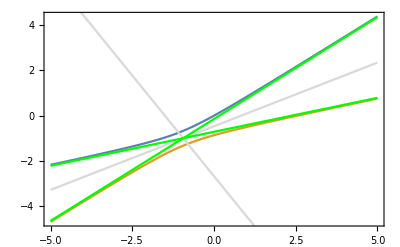

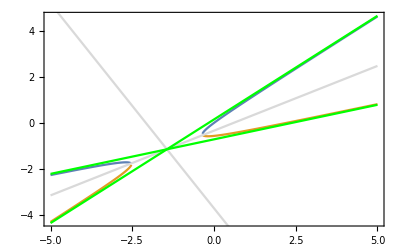

```mathematica
pltFun[0.5(2Pi),0.5(2Pi)]
pltFun[-0.5(2Pi),0.5(2Pi)]
```

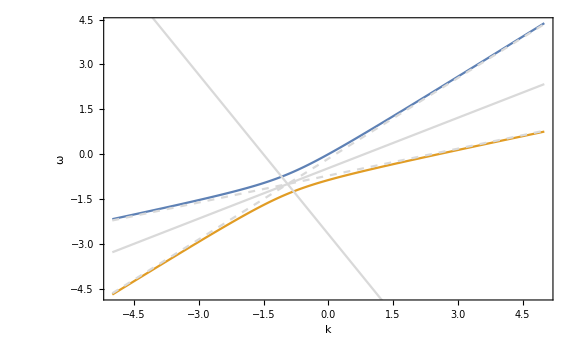

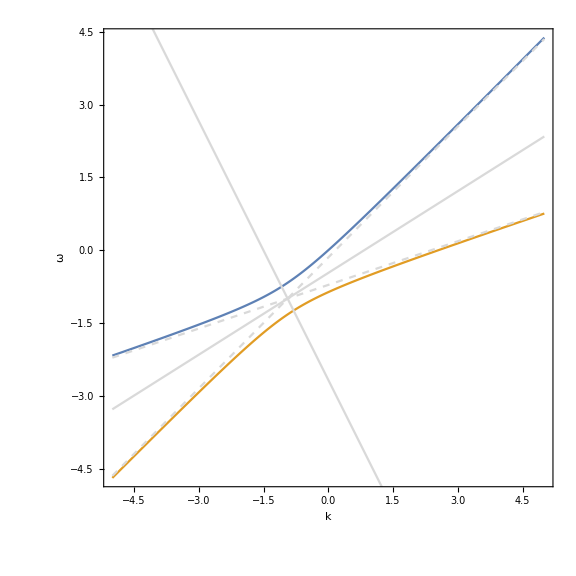

```mathematica
TwoBeamsAxialSymPlot[ArcCos@0.9,ArcCos@0.3,0.5(2Pi),0.5(2Pi)]
Show[TwoBeamsAxialSymPlot[ArcCos@0.9,ArcCos@0.3,0.5(2Pi),0.5(2Pi)],AspectRatio->1]
```

## Multiple Beams

```mathematica
beams2={
{-(2Pi)/2,ArcCos@0.9},
{(2Pi)/2,ArcCos@0.3}
}
beams4={
{-(2Pi)/4,ArcCos@0.9},
{-(2Pi)/4,ArcCos@0.7},
{(2Pi)/4,ArcCos@0.5},
{(2Pi)/4,ArcCos@0.3}
}
```

{{-π,0.451027},{π,1.2661}}

{{-π/2,0.451027},{-π/2,0.795399},{π/2,1.0472},{π/2,1.2661}}

```mathematica
NBeamsAxialSymOmegaKEqn[omega_,k_,beams_]:=4== Total[
(#[[1]](1-Cos[#[[2]]]^2) )/(omega-k Cos[#[[2]]])&/@beams
];
NBeamsAxialSymOmegaKPolyEqn[omega_,k_,beams_]:=4Apply[Times,(omega-k Cos[#[[2]]])&/@beams]== Total[
Table[
(beams[[i,1]](1-Cos[beams[[i,2]]]^2) )Apply[Times,(omega-k Cos[#[[2]]])&/@beams]/(omega-k Cos[beams[[i,2]]]),
{i,1,Length@beams}]
]
```

```mathematica
NBeamsAxialSymOmegaKEqn[omega,k,{{g1,theta1},{g2,theta2},{g3,theta3},{g4,theta4}}]
NBeamsAxialSymOmegaKPolyEqn[omega,k,{{g1,theta1},{g2,theta2},{g3,theta3},{g4,theta4}}]
```

4==(g1 (1-Cos[theta1]^2))/(omega-k Cos[theta1])+(g2 (1-Cos[theta2]^2))/(omega-k Cos[theta2])+(g3 (1-Cos[theta3]^2))/(omega-k Cos[theta3])+(g4 (1-Cos[theta4]^2))/(omega-k Cos[theta4])

4 (omega-k Cos[theta1]) (omega-k Cos[theta2]) (omega-k Cos[theta3]) (omega-k Cos[theta4])==g1 (1-Cos[theta1]^2) (omega-k Cos[theta2]) (omega-k Cos[theta3]) (omega-k Cos[theta4])+g2 (omega-k Cos[theta1]) (1-Cos[theta2]^2) (omega-k Cos[theta3]) (omega-k Cos[theta4])+g3 (omega-k Cos[theta1]) (omega-k Cos[theta2]) (1-Cos[theta3]^2) (omega-k Cos[theta4])+g4 (omega-k Cos[theta1]) (omega-k Cos[theta2]) (omega-k Cos[theta3]) (1-Cos[theta4]^2)

Analytically solve it

```mathematica
NBeamsAxialSymOmegaFunPoly[k_,beams_]:=omega/.{ToRules@Reduce[NBeamsAxialSymOmegaKPolyEqn[omega,k,beams],omega]}
```

Numerically solve it
with two different methods, the polynomial equation and the original equation

```mathematica
NBeamsAxialSymOmegaKPoly[k_,beams_]:=
omega/.NSolve[NBeamsAxialSymOmegaKPolyEqn[omega,k,beams],omega]
```

```mathematica
NBeamsAxialSymOmegaK[k_,beams_]:=
omega/.NSolve[NBeamsAxialSymOmegaKEqn[omega,k,beams],omega]
```

Now we have three methods, so we compare the three

Reduce method faster than NSolve polynomial faster than NSolve original equation

The best part of Reduce is that it keeps track of the branch of solutions. NSolve doesn’t.

```mathematica
NBeamsAxialSymOmegaFunPoly[0.4,beams2]//Timing
NBeamsAxialSymOmegaKPoly[0.4,beams2]//Timing
NBeamsAxialSymOmegaK[0.4,beams2]//Timing
```

{0.00221,{0.522743-0.0965855 ⅈ,0.522743+0.0965855 ⅈ}}

{0.00568,{0.522743-0.0965855 ⅈ,0.522743+0.0965855 ⅈ}}

{0.0123,{0.522743+0.0965855 ⅈ,0.522743-0.0965855 ⅈ}}

2 Beams Test

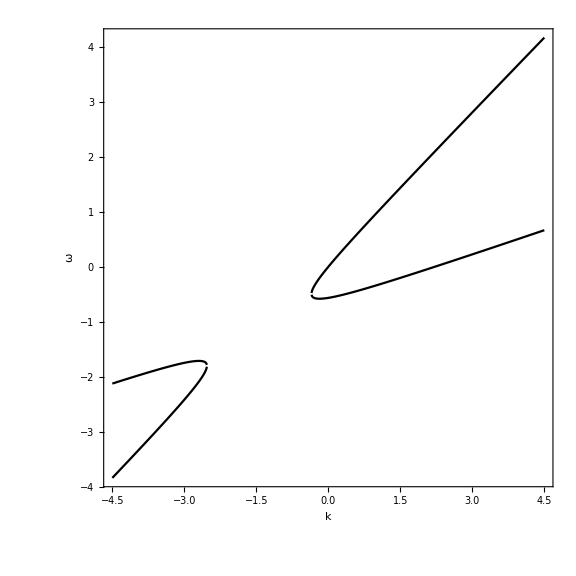

```mathematica
twoBeamsOmegaK=Table[
{k,#}&/@NBeamsAxialSymOmegaFunPoly[k,beams2],
{k,-4.5,4.5,0.01}];

twoBeamsOmegaKClean=DeleteCases[twoBeamsOmegaK,x_/;Length@x!=2];
%//Grid;
Transpose@twoBeamsOmegaKClean;

twoBeamsMAAPltEx1=ListPlot[-Transpose@twoBeamsOmegaKClean,Joined->True,Frame->True,FrameLabel->{"k","ω"},ImageSize->Large,PlotStyle->Black,AspectRatio->1]
```

Check the MZA solution

```mathematica
TwoBeamsAxialSymMZAOmegaKEqnPlus[omega_,k_,theta1_,theta2_,g1_,g2_]:=Module[{I0M,I1M,I2M},

I0M=g1/(omega-k Cos[theta1]) + g2/(omega-k Cos[theta2]);
I1M=g1 Cos[theta1]/(omega-k Cos[theta1]) + g2 Cos[theta2]/(omega-k Cos[theta2]);
I2M=g1 Cos[theta1]^2/(omega-k Cos[theta1]) + g2 Cos[theta2]^2/(omega-k Cos[theta2]);

-4==I0M-I2M+√((I0M-2I1M+I2M)(I0M+2I1M+I2M))

]
```

```mathematica
TwoBeamsAxialSymMZAOmegaKEqnPlus[omega,k,theta1,theta2,g1,g2]
```

```mathematica
-4==g1/(omega-k Cos[theta1])-(g1 Cos[theta1]^2)/(omega-k Cos[theta1])+g2/(omega-k Cos[theta2])-(g2 Cos[theta2]^2)/(omega-k Cos[theta2])+√((g1/(omega-k Cos[theta1])+(g1 Cos[theta1]^2)/(omega-k Cos[theta1])+g2/(omega-k Cos[theta2])+(g2 Cos[theta2]^2)/(omega-k Cos[theta2])-2 ((g1 Cos[theta1])/(omega-k Cos[theta1])+(g2 Cos[theta2])/(omega-k Cos[theta2]))) (g1/(omega-k Cos[theta1])+(g1 Cos[theta1]^2)/(omega-k Cos[theta1])+g2/(omega-k Cos[theta2])+(g2 Cos[theta2]^2)/(omega-k Cos[theta2])+2 ((g1 Cos[theta1])/(omega-k Cos[theta1])+(g2 Cos[theta2])/(omega-k Cos[theta2]))))
```

-4==g1/(omega-k Cos[theta1])-(g1 Cos[theta1]^2)/(omega-k Cos[theta1])+g2/(omega-k Cos[theta2])-(g2 Cos[theta2]^2)/(omega-k Cos[theta2])+√((g1/(omega-k Cos[theta1])+(g1 Cos[theta1]^2)/(omega-k Cos[theta1])+g2/(omega-k Cos[theta2])+(g2 Cos[theta2]^2)/(omega-k Cos[theta2])-2 ((g1 Cos[theta1])/(omega-k Cos[theta1])+(g2 Cos[theta2])/(omega-k Cos[theta2]))) (g1/(omega-k Cos[theta1])+(g1 Cos[theta1]^2)/(omega-k Cos[theta1])+g2/(omega-k Cos[theta2])+(g2 Cos[theta2]^2)/(omega-k Cos[theta2])+2 ((g1 Cos[theta1])/(omega-k Cos[theta1])+(g2 Cos[theta2])/(omega-k Cos[theta2]))))

```mathematica
TwoBeamsAxialSymMZAOmegaKEqnPlus[omega,k,ArcCos@0.9,ArcCos@0.3,-0.5(2Pi),0.5(2Pi)]//FullSimplify
```

0.596903/(-0.9 k+omega)==4+2.85885/(-0.3 k+omega)+√((25.9729 k^2+85.3904 k omega-124.771 omega^2)/((1. k^2-4.44444 k omega+3.7037 omega^2)^2))

```mathematica
twoBeamsMZAEqn1=(0.5969026041820604/(-0.9 k+omega)-4-2.858849314766712/(-0.29999999999999993 k+omega))(1. k^2-4.444444444444445 k omega+3.7037037037037046 omega^2)==√(25.972899680693935 k^2+85.39035511461019 k omega-124.77129514463591 omega^2)//FullSimplify
```

-4. k^2+(-8.37758-14.8148 omega) omega+k (8.86627+17.7778 omega)==√(25.9729 k^2+85.3904 k omega-124.771 omega^2)

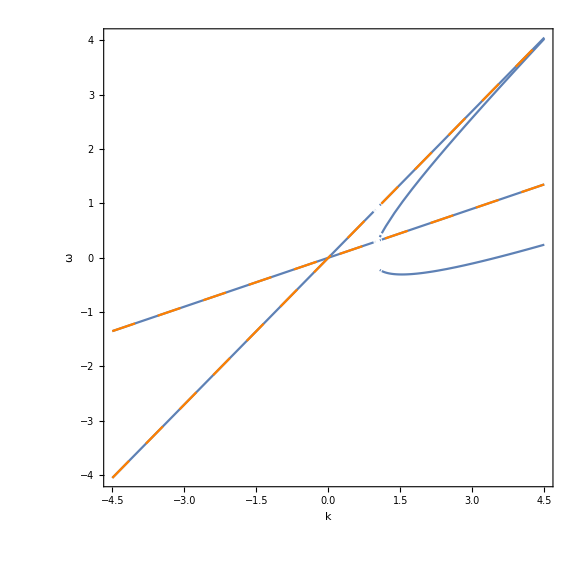

```mathematica
twoBeamsMZAPltEx1=Module[{eqnM,solM,dataM,plt1M,plt2M},

eqnM=twoBeamsMZAEqn1;

(*eqnM=156.52948886191894 k^2-494.86115235750106 k omega+358.7716277487902 omega^2==16. (1. k^2+k (2.5481807079117216-4.444444444444445 omega)+omega (-3.199770295322938+3.7037037037037046 omega))^2;
*)

(*TwoBeamsAxialSymMZAOmegaKEqnPlus[omega,k,ArcCos@0.9,ArcCos@0.3,0.5(2Pi),0.5(2Pi)]//FullSimplify;*)

solM[k_]=omega/.Solve[eqnM,omega];
(*dataM=Table[{k,solM[k]},{k,-5,5,0.1}]*)

(*ListPlot[dataM]*)

plt1M=Plot[solM[k],{k,-4.5,4.5},Frame->True,ImageSize->Large,FrameLabel->{"k","ω"}]//Quiet;
plt2M=Plot[{0.9x,0.3x},{x,-4.5,4.5},PlotStyle->Directive[Orange,Dashing[0.03]]];

Show[plt1M,plt2M,AspectRatio->1]

]
```

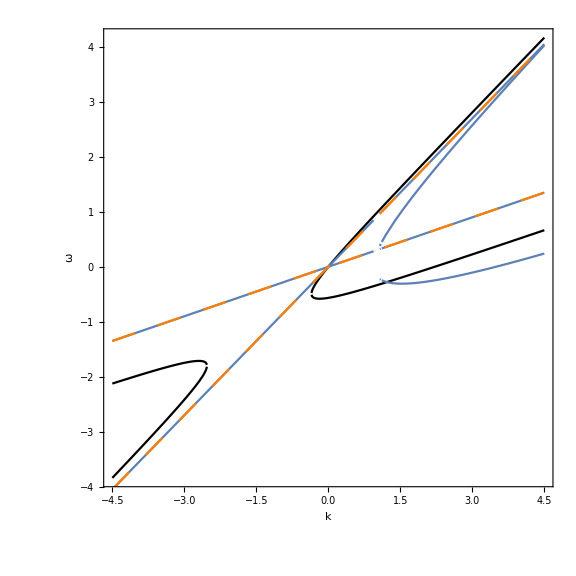

```mathematica
Show[twoBeamsMAAPltEx1,twoBeamsMZAPltEx1]
```

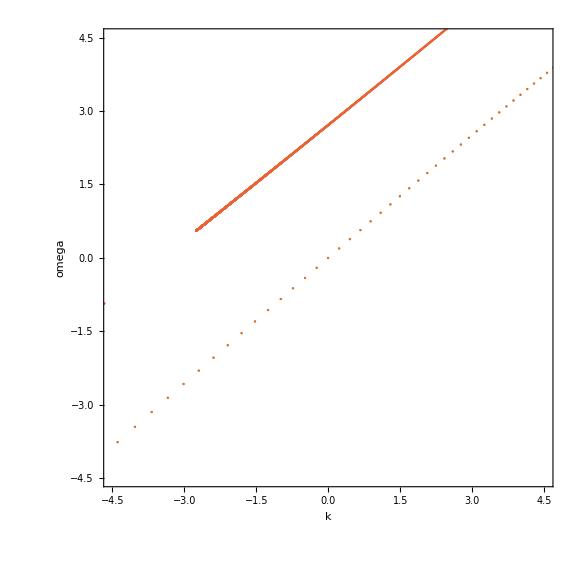

```mathematica
Module[{beamsM,dataM},


Show[dataPltNBeamsPlt[
Table[beams2[[i,1]],{i,1,2}],
Table[beams2[[i,2]],{i,1,2}],{-5,5},0.00099,{{-4.5,4.5},{-4.5,4.5}}],
AspectRatio->1]

(*dataM=Table[
Table[
{nM,
Eigenvalues[
nMatFunNBeams[Join[Table[(2Pi)/beamsM,{n,1,beamsM/2}],Table[2Pi/beamsM,{n,1,beamsM/2}]],nM,
Table[ArcCos@0.9+n (ArcCos@0.3-ArcCos@0.9)/(beamsM-1),{n,0,beamsM-1}]]
][[i]]},
{i,1,4}],
{nM,-5,5,0.09}
]//Transpose;
*)

(*ListPlot[dataM,Frame->True,ImageSize->Large]*)

]
```

Four Beams

```mathematica
fourBeamsOmegaK=Table[
-{k,#}&/@NBeamsAxialSymOmegaFunPoly[k,beams4],
{k,-4.5,10,0.001}];

fourBeamsOmegaKClean=DeleteCases[fourBeamsOmegaK,x_/;Length@x≠Length@beams4];
%//Grid;
Transpose@fourBeamsOmegaKClean;
```

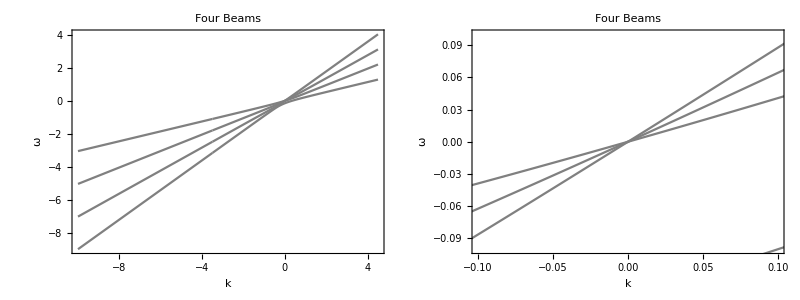

```mathematica
{{fourBeamsOmegaKPlt1=ListPlot[Transpose@fourBeamsOmegaKClean,Joined->True,Frame->True,FrameLabel->{"k","ω"},ImageSize->Large,PlotLabel->"Four Beams",PlotStyle->Gray],
Show[fourBeamsOmegaKPlt1,PlotRange->{{-0.1,0.1},{-0.1,0.1}}]}}//Grid
```

```mathematica
fourBeamSigularity=Plot[(Transpose@beams4)[[2]]x,{x,-10,4.5},PlotStyle->Directive[Orange,Dashing[0.03]]];
fourBeamSigularity0=Plot[{0.35x,-0.349x},{x,-10,4.5},PlotStyle->Directive[Orange,Dashing[0.03]]];
```

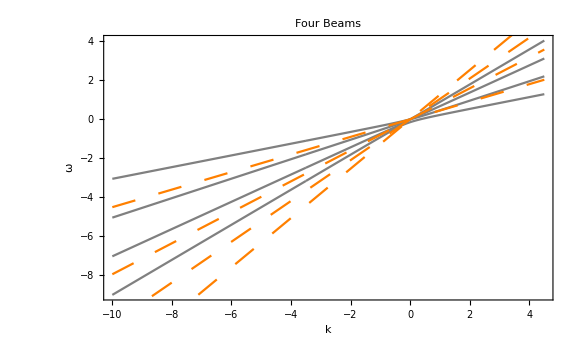

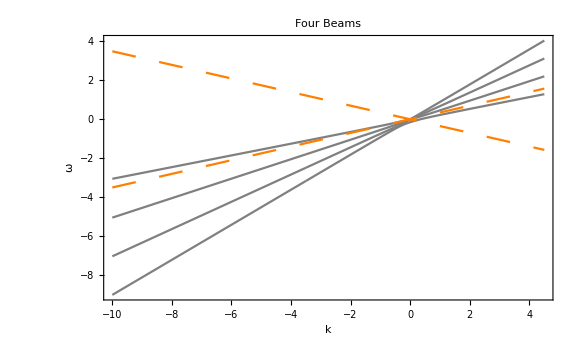

```mathematica
Show[fourBeamsOmegaKPlt1,fourBeamSigularity]
Show[fourBeamsOmegaKPlt1,fourBeamSigularity0]
```

I can cacluate using the omega(n) method

```mathematica
beams4
```

{{π/2,0.451027},{π/2,0.795399},{π/2,1.0472},{π/2,1.2661}}

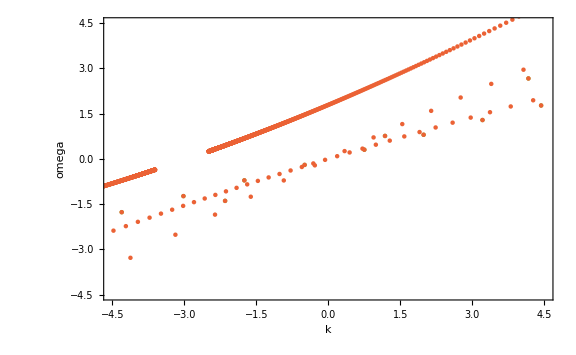

```mathematica
Module[{beamsM,dataM},


Show[dataPltNBeamsPlt[
Table[beams4[[i,1]],{i,1,4}],
Table[beams4[[i,2]],{i,1,4}],{-10,10},0.0099,{{-4.5,4.5},{-4.5,4.5}}]
]

(*dataM=Table[
Table[
{nM,
Eigenvalues[
nMatFunNBeams[Join[Table[(2Pi)/beamsM,{n,1,beamsM/2}],Table[2Pi/beamsM,{n,1,beamsM/2}]],nM,
Table[ArcCos@0.9+n (ArcCos@0.3-ArcCos@0.9)/(beamsM-1),{n,0,beamsM-1}]]
][[i]]},
{i,1,4}],
{nM,-5,5,0.09}
]//Transpose;
*)

(*ListPlot[dataM,Frame->True,ImageSize->Large]*)

]
```

8 Beams

```mathematica
NBeamsLR[beams_]:=Module[{hombmM},

hombmM=Transpose[
({(2Pi)/beams,#}&/@Table[ArcCos[0.9+beam(-0.9+0.3)/(beams-1)],{beam,0,beams-1}])
];


hombmM[[1]]=Join[
Table[-1(hombmM)[[1,i]],{i,1,beams/2}],
Table[(hombmM)[[1,i]],{i,beams/2+1,beams}]
];

Transpose@hombmM

]
```

```mathematica
NBeamsLR[2]
beams2
NBeamsLR[4]
beams4
```

{{-π,0.451027},{π,1.2661}}

{{-π,0.451027},{π,1.2661}}

{{-π/2,0.451027},{-π/2,0.795399},{π/2,1.0472},{π/2,1.2661}}

{{-π/2,0.451027},{-π/2,0.795399},{π/2,1.0472},{π/2,1.2661}}

```mathematica
beams8=NBeamsLR[8]
```

{{-π/4,0.451027},{-π/4,0.619299},{-π/4,0.754562},{-π/4,0.872574},{π/4,0.979855},{π/4,1.07989},{π/4,1.17481},{π/4,1.2661}}

```mathematica
Module[{beamsomegaKM,beamsOmegaKCleanM,beamsOmegaKPltM,nbeamsM,beamsSingularityM},

nbeamsM=8;

beamsomegaKM=Table[
-{k,#}&/@NBeamsAxialSymOmegaFunPoly[k,NBeamsLR[nbeamsM]],
{k,-4.5,10,0.01}];

beamsOmegaKCleanM=DeleteCases[beamsomegaKM,x_/;Length@x≠nbeamsM];

Transpose@beamsOmegaKCleanM;

beamsSingularityM=Plot[(Transpose@NBeamsLR[nbeamsM])[[2]]x,{x,-10,10},PlotStyle->Directive[Orange,Dashing[0.03]]];

{{beamsOmegaKPltM=ListPlot[beamsomegaKM,Joined->False,Frame->True,FrameLabel->{"k","ω"},ImageSize->Large,PlotLabel->ToString@nbeamsM<>" Beams",PlotStyle->Gray],
Show[beamsOmegaKPltM,beamsSingularityM],
Show[beamsOmegaKPltM,PlotRange->{{-0.1,0.1},{-0.1,0.1}}]
}}//Grid

]
```

N Beams

```mathematica
nBeamsLRPlt[nbeams_,kRange_:{-4.5,4.5}]:=Module[{beamsomegaKM,beamsOmegaKCleanM,beamsOmegaKPltM,nbeamsM,beamsSingularityM},

nbeamsM=nbeams;

beamsomegaKM=Table[
-{k,#}&/@NBeamsAxialSymOmegaFunPoly[k,NBeamsLR[nbeamsM]],
{k,-kRange[[2]],-kRange[[1]],0.01}];


(*
beamsomegaKM=Table[
-{k,#}&/@NBeamsAxialSymOmegaKPoly[k,NBeamsLR[nbeamsM]],
{k,-4.5,4.5,0.01}];*)


beamsOmegaKCleanM=DeleteCases[beamsomegaKM,x_/;Length@x≠nbeamsM];

Transpose@beamsOmegaKCleanM;

beamsSingularityM=Plot[(Transpose@Cos@NBeamsLR[nbeamsM])[[2]]x,{x,kRange[[1]],kRange[[2]]},PlotStyle->Directive[Orange,Dashing[0.03]]];

{{beamsOmegaKPltM=ListPlot[beamsomegaKM,Joined->False,Frame->True,FrameLabel->{"k","ω"},ImageSize->Large,PlotLabel->ToString@nbeamsM<>" Beams",PlotStyle->Gray,PlotRange->{kRange,Automatic}],
Show[beamsOmegaKPltM,beamsSingularityM],
Show[beamsOmegaKPltM,PlotRange->{{-0.1,0.1},{-0.1,0.1}}]
}}

]
```

```mathematica
nBeamsLRPlt2[nbeams_,kRange_:{-4.5,4.5}]:=Module[{beamsomegaKM,beamsOmegaKCleanM,beamsOmegaKPltM,nbeamsM,beamsSingularityM},

nbeamsM=nbeams;

beamsomegaKM=Table[
-{k,#}&/@NBeamsAxialSymOmegaFunPoly[k,nbeamsM],
{k,-kRange[[2]],-kRange[[1]],0.01}];


(*
beamsomegaKM=Table[
-{k,#}&/@NBeamsAxialSymOmegaKPoly[k,NBeamsLR[nbeamsM]],
{k,-4.5,4.5,0.01}];*)


beamsOmegaKCleanM=DeleteCases[beamsomegaKM,x_/;Length@x≠Length@nbeamsM];

Transpose@beamsOmegaKCleanM;

beamsSingularityM=Plot[(Transpose@Cos@nbeamsM)[[2]]x,{x,kRange[[1]],kRange[[2]]},PlotStyle->Directive[Orange,Dashing[0.03]]];

{beamsOmegaKPltM=ListPlot[beamsomegaKM,Joined->False,Frame->True,FrameLabel->{"k","ω"},ImageSize->Large,PlotLabel->ToString@Length@nbeamsM<>" Beams",PlotStyle->Gray,PlotRange->{kRange,Automatic}],
Show[beamsOmegaKPltM,beamsSingularityM],
beamsomegaKM
}

]
```

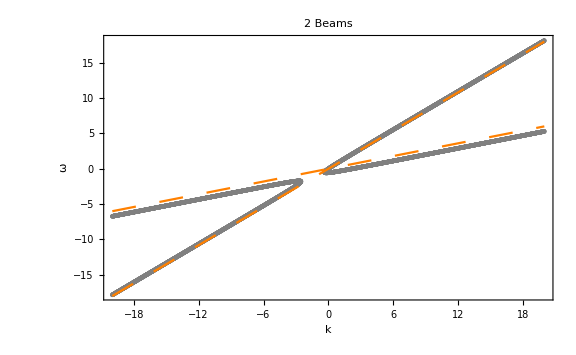

```mathematica
nBeamsLRPlt2[NBeamsLR[2],{-20,20}][[2]]
```

## The Limiting Behavior

```mathematica
NBeamsLR[2]
```

{{-π,0.451027},{π,1.2661}}

```mathematica
nBeamsOmegaNPlt[nbeams_,nRange_:{-4.5,4.5}]:=Module[{beamsomegaKM,omeganM,beamsOmegaKCleanM,beamsOmegaKPltM,nbeamsM,beamsSingularityM,gridlinesM},

nbeamsM=nbeams;

omeganM[n_]:=-1/4 Total[
(#[[1]](1-Cos[#[[2]]])/(1-n Cos[#[[2]]]))&/@nbeamsM
];

gridlinesM=1/Cos[#[[2]]]&/@nbeams;

beamsOmegaKPltM=Plot[omeganM[n],{n,nRange[[1]],nRange[[2]]},Frame->True,FrameLabel->{"n","ω"},ImageSize->Large,PlotLabel->"Beams: "<>ToString@Length@nbeamsM,PlotStyle->Gray,PlotRange->{nRange,{-10,10}},Exclusions->gridlinesM];

Show[beamsOmegaKPltM,GridLines->{gridlinesM,None}]


]
```

```mathematica
NBeamsLR[2]
Cos@#[[2]]&/@%
```

{{-π,0.451027},{π,1.2661}}

{0.9,0.3}

```mathematica
nBeamsOmegaNPlt[NBeamsLR[2]]
```

nBeamsOmegaNPlt[{{-π,0.451027},{π,1.2661}}]

```mathematica
fourExample1=nBeamsLRPlt[2,{-20,20}];
```

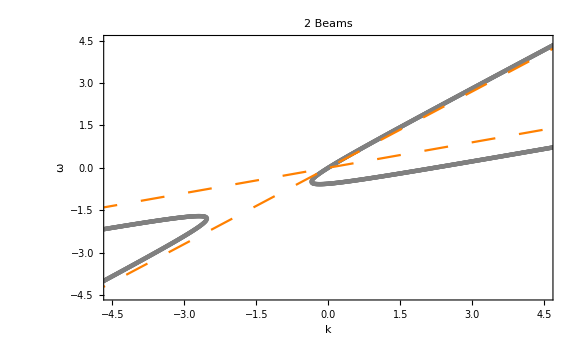

```mathematica
Show[fourExample1[[1,2]],PlotRange->{{-4.5,4.5},{-4.5,4.5}}]
```

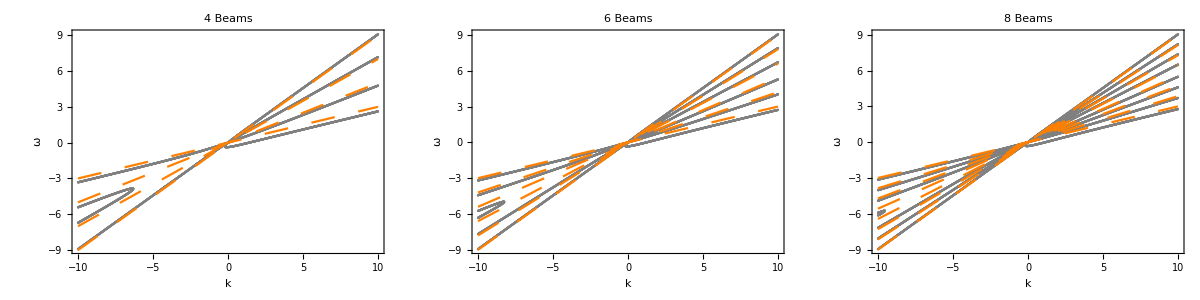

```mathematica
{{nBeamsLRPlt[4,{-10,10}][[1,2]],
nBeamsLRPlt[6,{-10,10}][[1,2]],
nBeamsLRPlt[8,{-10,10}][[1,2]]}}//Grid
```

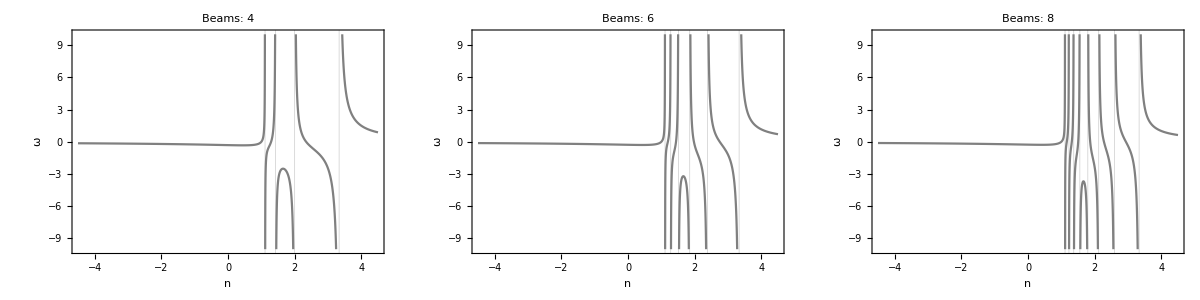

```mathematica
{{nBeamsOmegaNPlt[NBeamsLR[4]],
nBeamsOmegaNPlt[NBeamsLR[6]],
nBeamsOmegaNPlt[NBeamsLR[8]]}}//Grid
```

```mathematica
Cos@#[[2]]&/@NBeamsLR[4]
```

{0.9,0.7,0.5,0.3}

## Verification Code

First of all we have to build the arbitary N beams system

```mathematica
NBeamsEx1[beams_]:=Table[{(2Pi)/beams,ArcCos[0.9+beam(-0.9+0.3)/(beams-1)]},{beam,0,beams-1}]
NBeamsEx2[beams_]:=Table[{(2Pi)/beams,ArcCos@0.9+beam(ArcCos@0.3-ArcCos@0.9)/(beams-1)},{beam,0,beams-1}]
```

```mathematica
NBeamsEx1[10]
```

{{π/5,0.451027},{π/5,0.585686},{π/5,0.697163},{π/5,0.795399},{π/5,0.884943},{π/5,0.968342},{π/5,1.0472},{π/5,1.12261},{π/5,1.19537},{π/5,1.2661}}

```mathematica
NBeamsEx1[4]
NBeamsEx2[4]
beams4
```

{{π/2,0.451027},{π/2,0.795399},{π/2,1.0472},{π/2,1.2661}}

{{π/2,0.451027},{π/2,0.722719},{π/2,0.994411},{π/2,1.2661}}

{{π/2,0.451027},{π/2,0.795399},{π/2,1.0472},{π/2,1.2661}}

```mathematica
NBeamsAxialSymOmegaFunPoly[k,NBeamsEx1[4]]
NBeamsAxialSymOmegaFunPoly[k,beams4]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{Root[3.0226×10^77 k^3+1.40635×10^77 k^4+(-1.58517×10^78 k^2-1.10722×10^78 k^3) #1+(2.62286×10^78 k+3.0657×10^78 k^2) #1^2+(-1.37922×10^78-3.57169×10^78 k) #1^3+1.48821×10^78 #1^4&,1],Root[3.0226×10^77 k^3+1.40635×10^77 k^4+(-1.58517×10^78 k^2-1.10722×10^78 k^3) #1+(2.62286×10^78 k+3.0657×10^78 k^2) #1^2+(-1.37922×10^78-3.57169×10^78 k) #1^3+1.48821×10^78 #1^4&,2],Root[3.0226×10^77 k^3+1.40635×10^77 k^4+(-1.58517×10^78 k^2-1.10722×10^78 k^3) #1+(2.62286×10^78 k+3.0657×10^78 k^2) #1^2+(-1.37922×10^78-3.57169×10^78 k) #1^3+1.48821×10^78 #1^4&,3],Root[3.0226×10^77 k^3+1.40635×10^77 k^4+(-1.58517×10^78 k^2-1.10722×10^78 k^3) #1+(2.62286×10^78 k+3.0657×10^78 k^2) #1^2+(-1.37922×10^78-3.57169×10^78 k) #1^3+1.48821×10^78 #1^4&,4]}

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{Root[3.0226×10^77 k^3+1.40635×10^77 k^4+(-1.58517×10^78 k^2-1.10722×10^78 k^3) #1+(2.62286×10^78 k+3.0657×10^78 k^2) #1^2+(-1.37922×10^78-3.57169×10^78 k) #1^3+1.48821×10^78 #1^4&,1],Root[3.0226×10^77 k^3+1.40635×10^77 k^4+(-1.58517×10^78 k^2-1.10722×10^78 k^3) #1+(2.62286×10^78 k+3.0657×10^78 k^2) #1^2+(-1.37922×10^78-3.57169×10^78 k) #1^3+1.48821×10^78 #1^4&,2],Root[3.0226×10^77 k^3+1.40635×10^77 k^4+(-1.58517×10^78 k^2-1.10722×10^78 k^3) #1+(2.62286×10^78 k+3.0657×10^78 k^2) #1^2+(-1.37922×10^78-3.57169×10^78 k) #1^3+1.48821×10^78 #1^4&,3],Root[3.0226×10^77 k^3+1.40635×10^77 k^4+(-1.58517×10^78 k^2-1.10722×10^78 k^3) #1+(2.62286×10^78 k+3.0657×10^78 k^2) #1^2+(-1.37922×10^78-3.57169×10^78 k) #1^3+1.48821×10^78 #1^4&,4]}

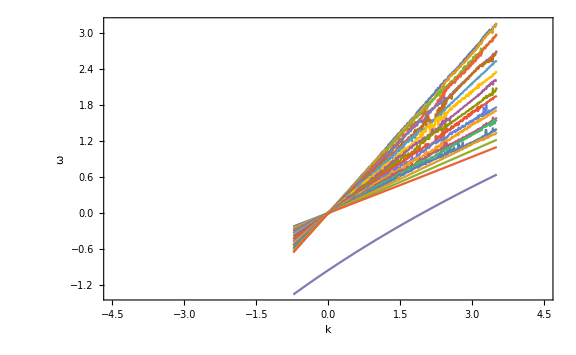

```mathematica
Module[{numBeamsM},
numBeamsM=20;

NBeamsOmegaK=Table[
{k,#}&/@NBeamsAxialSymOmegaFunPoly[k,NBeamsEx1[numBeamsM]],
{k,-4.5,4.5,0.01}];

NBeamsOmegaKClean=DeleteCases[NBeamsOmegaK,x_/;Length@x≠Length@NBeamsEx1[numBeamsM]];
%//Grid;
Transpose@NBeamsOmegaKClean;

ListPlot[-Transpose@NBeamsOmegaKClean,Joined->True,Frame->True,FrameLabel->{"k","ω"},ImageSize->Large,PlotRange->{{-4.5,4.5},Automatic}]
]
```

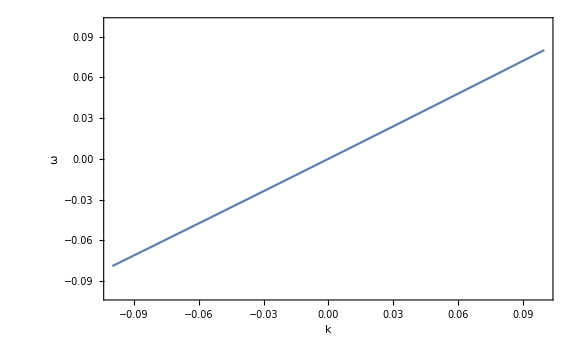
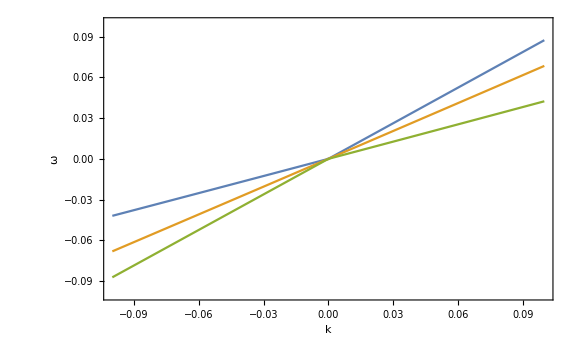
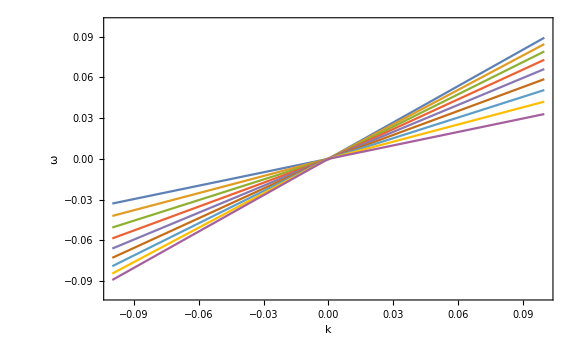
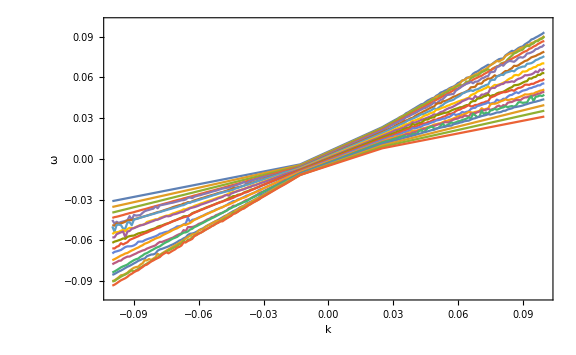
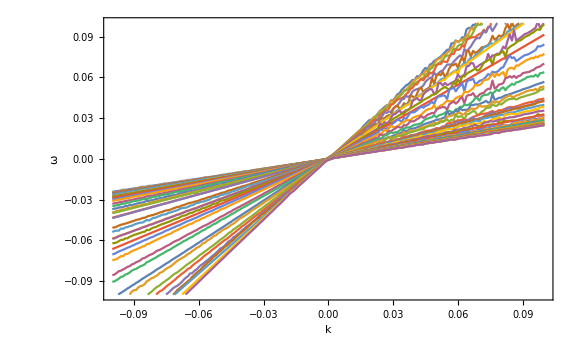
Grid[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]

```mathematica
Table[
Module[{numBeamsM,rangeM},
numBeamsM=numberofbeams;
rangeM={-0.1,0.1};

NBeamsOmegaK=Table[
{k,#}&/@NBeamsAxialSymOmegaFunPoly[k,NBeamsEx1[numBeamsM]],
{k,rangeM[[1]],rangeM[[2]],0.001}];

NBeamsOmegaKClean=DeleteCases[NBeamsOmegaK,x_/;Length@x≠Length@NBeamsEx1[numBeamsM]];
%//Grid;
Transpose@NBeamsOmegaKClean;

ListPlot[-Transpose@NBeamsOmegaKClean,Joined->True,Frame->True,FrameLabel->{"k","ω"},ImageSize->Large,PlotRange->{rangeM,rangeM}]
],
{numberofbeams,{2,4,10,20,40}}]//Grid
```

This result looks doubtful. I can verify it using other methods.

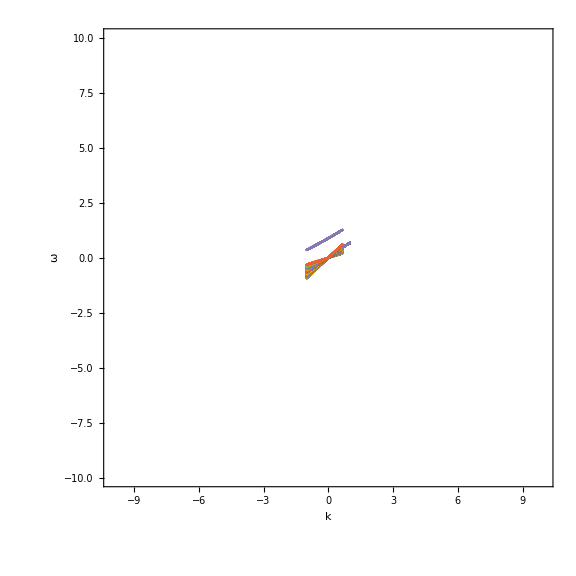

```mathematica
Module[{numBeamsM,NBeamsOmegaKM,NBeamsOmegaKCleanM},
numBeamsM=20;

NBeamsOmegaKM=Table[
{k,#}&/@NBeamsAxialSymOmegaKPoly[k,NBeamsEx1[numBeamsM]],
{k,-1,1,0.01}];

NBeamsOmegaKCleanM=DeleteCases[NBeamsOmegaKM,x_/;Length@x≠Length@NBeamsEx1[numBeamsM]];
%//Grid;
Transpose@NBeamsOmegaKCleanM;

ListPlot[Transpose@NBeamsOmegaKCleanM,Joined->False,Frame->True,FrameLabel->{"k","ω"},ImageSize->Large,PlotRange->{{-10,10},{-10,10}},AspectRatio->1]
]
```

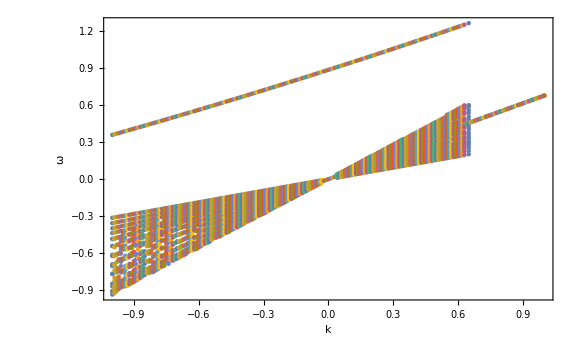

```mathematica
Module[{numBeamsM,NBeamsOmegaKM},
numBeamsM=20;

NBeamsOmegaKM=Table[
{k,#}&/@NBeamsAxialSymOmegaFunPoly[k,NBeamsEx1[numBeamsM]],
{k,-1,1,0.01}];

(*NBeamsOmegaKClean=DeleteCases[NBeamsOmegaK,x_/;Length@x≠Length@NBeamsEx1[numBeamsM]];
%//Grid;
Transpose@NBeamsOmegaKClean;
*)
ListPlot[NBeamsOmegaKM,Joined->False,Frame->True,FrameLabel->{"k","ω"},ImageSize->Large,PlotRange->{{-1,1},Automatic}]
]
```

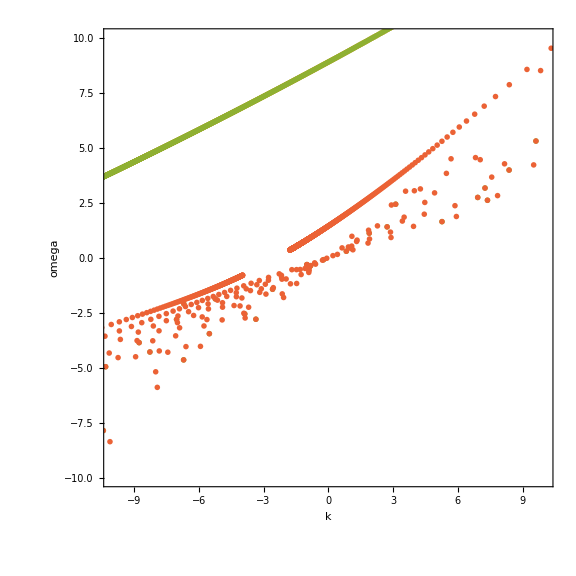

```mathematica
Module[{beamsM,dataM},

beamsM=20;


Show[dataPltNBeamsPlt[
Join[Table[(2Pi)/beamsM,{n,1,beamsM/2}],Table[(2Pi)/beamsM,{n,1,beamsM/2}]],
Table[ArcCos@0.9+n(ArcCos@0.3-ArcCos@0.9)/(beamsM-1),{n,0,beamsM-1}],{-5,5},0.009,{{-10,10},{-10,10}}],AspectRatio->1]

(*dataM=Table[
Table[
{nM,
Eigenvalues[
nMatFunNBeams[Join[Table[(2Pi)/beamsM,{n,1,beamsM/2}],Table[2Pi/beamsM,{n,1,beamsM/2}]],nM,
Table[ArcCos@0.9+n (ArcCos@0.3-ArcCos@0.9)/(beamsM-1),{n,0,beamsM-1}]]
][[i]]},
{i,1,4}],
{nM,-5,5,0.09}
]//Transpose;
*)

(*ListPlot[dataM,Frame->True,ImageSize->Large]*)

]
```